```mathematica
GaussianFilter[-Graphics-, 20]
```

-Graphics-

```mathematica
FindFaces[-Graphics-]
```

{Rectangle[{187.5,363.5},{219.5,407.5}],Rectangle[{334.5,345.5},{365.5,387.5}],Rectangle[{443.5,402.5},{475.5,444.5}],Rectangle[{243.5,350.5},{275.5,393.5}],Rectangle[{374.5,264.5},{417.5,319.5}],Rectangle[{255.5,402.5},{282.5,437.5}],Rectangle[{123.5,207.5},{163.5,259.5}],Rectangle[{174.5,289.5},{215.5,336.5}],Rectangle[{64.5,339.5},{97.5,379.5}],Rectangle[{515.5,283.5},{550.5,330.5}],Rectangle[{592.5,260.5},{638.5,322.5}],Rectangle[{518.5,363.5},{551.5,404.5}],Rectangle[{171.5,442.5},{197.5,478.5}],Rectangle[{200.5,419.5},{228.5,457.5}],Rectangle[{298.5,436.5},{326.5,472.5}],Rectangle[{498.5,162.5},{545.5,216.5}],Rectangle[{72.5,256.5},{118.5,315.5}],Rectangle[{236.5,254.5},{283.5,310.5}],Rectangle[{109.5,307.5},{143.5,350.5}],Rectangle[{488.5,335.5},{519.5,376.5}],Rectangle[{431.5,312.5},{469.5,359.5}],Rectangle[{209.5,145.5},{251.5,203.5}],Rectangle[{92.5,409.5},{124.5,447.5}],Rectangle[{575.5,403.5},{607.5,444.5}],Rectangle[{415.5,208.5},{458.5,262.5}],Rectangle[{134.5,398.5},{160.5,433.5}],Rectangle[{351.5,405.5},{380.5,441.5}],Rectangle[{403.5,432.5},{431.5,469.5}],Rectangle[{570.5,310.5},{605.5,358.5}],Rectangle[{396.5,376.5},{432.5,417.5}],Rectangle[{482.5,245.5},{522.5,299.5}],Rectangle[{518.5,407.5},{544.5,440.5}],Rectangle[{297.5,291.5},{337.5,335.5}],Rectangle[{572.5,179.5},{618.5,236.5}],Rectangle[{310.5,210.5},{355.5,270.5}]}

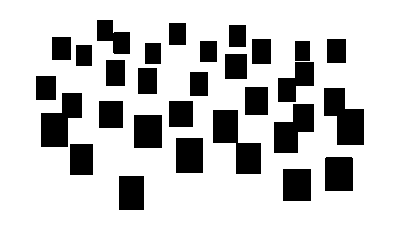

```mathematica
Graphics[%]
```

```mathematica
Array[f, 10]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

```mathematica
Array[## &, {10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Fold[f, 0 , {1, 2, 3}]
```

f[f[f[0,1],2],3]

```mathematica
Map[Abs, {-1, -3}]
```

{1,3}

### Lazy evaluation

```mathematica
t := Now
```

```mathematica
t
```

Tue 3 Aug 2021 18:39:41GMT-6

```mathematica
t
```

Tue 3 Aug 2021 18:39:48GMT-6

```mathematica
Table[i, {i, 1, 10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
andrey[n_Integer] := n + 1;
andrey[n_Real] := n  * 10;
```

```mathematica
andrey[1]
```

2

```mathematica
andrey[10.5]
```

105.

## Listas

```mathematica
l1 = {1, 2, 3}
```

{1,2,3}

```mathematica
l1[[1]]
```

1

```mathematica
First[l1]
```

1

```mathematica
Rest[l1]
```

{2,3}

```mathematica
Most[l1]
```

{1,2}

```mathematica
Drop[l1, -2]
```

{1}

```mathematica
Take[l1, {2, 3}]
```

{2,3}

## Funciones

```mathematica
Sumar[n1_,n2_ ] := n1 + n2
```

```mathematica
Sumar[1, 4]
```

5

```mathematica
Function[n, n + 2][4]
```

6

```mathematica
Array[Function[u, u u], {10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
# # & [18]
```

324

```mathematica
Array[# # &, {10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
r = #1 + #2 + #3 &
```

#1+#2+#3&

```mathematica
r[2, 3, 4]
```

9

## Fibonacci

```mathematica
Fibo[0] = 0;
Fibo[1] = 1;
Fibo[n_] := Fibo[n -1 ] + Fibo[n - 2]
```

```mathematica
Fibo[7]
```

13

```mathematica
Table[Fibo[x], {x, 0, 10}]
```

{0,1,1,2,3,5,8,13,21,34,55}

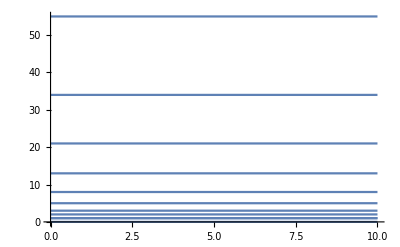

```mathematica
Plot[Table[Fibo[x], {x, 0, 10}], {x, 0 , 10}]
```